```mathematica
VelsRaw=Import["/Users/shaviv/MyDrive/Professional/Research/Astro/Eddington/Raman-eta-Carinae/Velocity_distribution/v_vs_theta.csv"];
```

```mathematica
vsDeg=Interpolation[VelsRaw[[2;;,1;;2]]]
```

InterpolatingFunction[…]

```mathematica
bounds=7;imsize=250;
```

```mathematica
vs[θ_]:=vsDeg[Abs[90-Mod[θ,π]*180/π]]
```

```mathematica
Circ[rout_,fill_,boundary_]:=RegionPlot[Sqrt[x^2+y^2] < rout, {x,-5,5},{y,-5,5},AspectRatio->1, BoundaryStyle->boundary, PlotStyle->fill,Frame->None, PlotPoints->120]
```

```mathematica
CircOff[rout_,fill_,boundary_, xoff_, yoff_]:=RegionPlot[Sqrt[(x-xoff)^2+(y-yoff)^2] < rout, {x,-5,5},{y,-5,5},AspectRatio->1, BoundaryStyle->boundary, PlotStyle->fill,Frame->None, PlotPoints->120]
```

```mathematica
Homun[rin_,rout_,offsetin_,offsetout_,fill_,boundary_]:=RegionPlot[offsetin+ vs[ArcTan[x/y]]/650  rin<Sqrt[x^2+y^2] <offsetout+ vs[ArcTan[x/y]]/650  rout, {x,-bounds/2,bounds/2},{y,-bounds,bounds},AspectRatio->2, BoundaryStyle->boundary, PlotStyle->fill,Frame->None,PlotPoints->100]
```

```mathematica
WigglyArrow[p1_,α_,l_,n_,sy_,ps_,th_]:=Module[{},
xs =l Table[i,{i,0,1,1/ps}];
ys = Table[ sy Sin[2π n  i],{i,0,1,1/ps}];
Show[ListPlot[Transpose[{p1[[1]]+Cos[α]xs-Sin[α]ys,p1[[2]]+Sin[α]xs+Cos[α]ys}],Joined->True,AspectRatio->1,Axes->None,PlotStyle->Directive[Black,Thickness[th]]],
Graphics[{Arrowheads[Medium],Thickness[th],Arrow[{{p1[[1]]+Cos[α]l,p1[[2]]+Sin[α]l},{p1[[1]]+Cos[α](l+0.25),p1[[2]]+Sin[α](l+0.25)}}]}]]
]
```

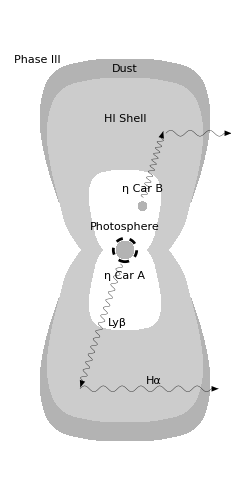

```mathematica
p3=Show[
Homun[5.0,6,0.85,0.5,GrayLevel[0.7],None],
Homun[2.25,5,0.5,0.85,GrayLevel[0.8],None], 
Circ[0.3,GrayLevel[0.7],None],
Circ[0.4,None,Directive[Black,Dashed]],
CircOff[0.15,GrayLevel[0.7],None, 0.6,1.5],
WigglyArrow[0.5{-Cos[0.8 π/2],-Sin[0.8 π/2]},-π/2(1+0.2),4.2,15,0.10,200,0.001],
WigglyArrow[5.0{-Cos[0.8 π/2],-Sin[0.8 π/2]},0,4.5,7,0.10,200,0.001],
WigglyArrow[0.9{0.7,2.0},ArcTan[0.6,2.0],Sqrt[0.7^2+2.0^2],10,0.10,200,0.001],
WigglyArrow[2.0{0.7,2.0},0,2.0,3,0.10,200,0.001],
Graphics[{Text["η Car A",{0,-0.9},Background->White],
Text["η Car B",{0.6,2.1},Background->White],
Text["Photosphere",{0,+0.8}],
Text["HI Shell",{0,+4.5}],
Text["Phase III",{-3,6.5}],
Text["Lyβ",{-0.25,-2.5}],
Text["Hα",{1,-4.5}],
Text["Dust", {0,6.2}]}],
ImageSize->imsize]
```

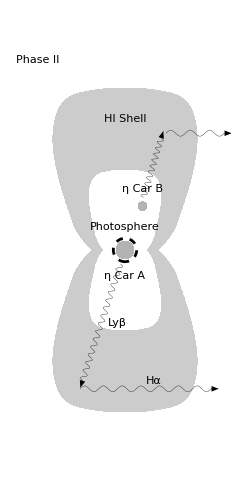

```mathematica
p2=Show[
Homun[2.25,5,0.5,0.5,GrayLevel[0.8],None], 
Circ[0.3,GrayLevel[0.7],None],
Circ[0.4,None,Directive[Black,Dashed]],
CircOff[0.15,GrayLevel[0.7],None, 0.6,1.5],
WigglyArrow[0.5{-Cos[0.8 π/2],-Sin[0.8 π/2]},-π/2(1+0.2),4.2,15,0.10,200,0.001],
WigglyArrow[5.0{-Cos[0.8 π/2],-Sin[0.8 π/2]},0,4.5,7,0.10,200,0.001],
WigglyArrow[0.9{0.7,2.0},ArcTan[0.6,2.0],Sqrt[0.7^2+2.0^2],10,0.10,200,0.001],
WigglyArrow[2.0{0.7,2.0},0,2.0,3,0.10,200,0.001],
Graphics[{Text["η Car A",{0,-0.9},Background->White],
Text["η Car B",{0.6,2.1},Background->White],
Text["Photosphere",{0,+0.8}],
Text["HI Shell",{0,+4.5}],
Text["Phase II",{-3,6.5}],
Text["Lyβ",{-0.25,-2.5}],
Text["Hα",{1,-4.5}]}],
ImageSize->imsize]
```

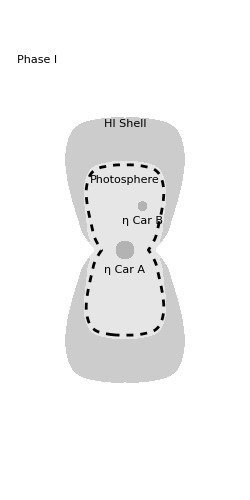

```mathematica
p1=Show[Homun[0,4,0.3,0.5,GrayLevel[0.9],None],
Homun[2.25,4,0.8,0.5,GrayLevel[0.8],None],
Circ[0.3,GrayLevel[0.7],None],
CircOff[0.15,GrayLevel[0.7],None, 0.6,1.5],
Homun[0,2.4,0,0.5,None,Directive[Black,Dashed]],
Graphics[{Text["η Car A",{0,-0.7}],
Text["η Car B",{0.6,1.0}],
Text["Photosphere",{0,+2.4}],
Text["Phase I",{-3,6.5}],
Text["HI Shell",{0,+4.3}]}],ImageSize->imsize]
```

```mathematica
Export["Raman_Phase1.pdf",Rasterize[p1,ImageResolution->600],"PDF"]
```

Raman_Phase1.pdf

```mathematica
Export["Raman_Phase2.pdf",Rasterize[p2,ImageResolution->600],"PDF"]
```

Raman_Phase2.pdf

```mathematica
Export["Raman_Phase3.pdf",Rasterize[p3,ImageResolution->600],"PDF"]
```

Raman_Phase3.pdf